# Plots Meta-community

```mathematica
filebase="/Users/ailenemacpherson/Documents/VisualStudio/metacommunity";
```

```mathematica
run=1;
```

## Parameters

```mathematica
pars=Import[filebase<>"/run_"<>ToString[run]<>"/out.csv"];
```

```mathematica
gmax=pars[[1,2]];
xmax=pars[[2,2]];
ymax=pars[[3,2]];
```

```mathematica
nb=pars[[5+ymax,2]];
nh=pars[[6+ymax,2]];
np=pars[[7+ymax,2]];
```

```mathematica
LMtrx=pars[[5;;4+ymax,;;xmax]];
```

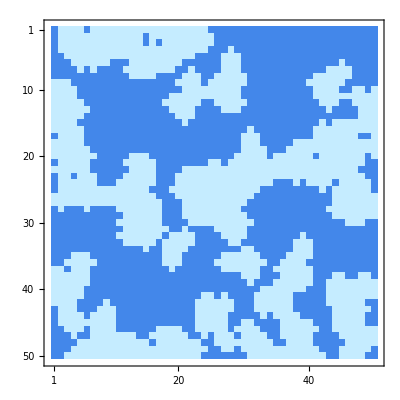

```mathematica
MatrixPlot[Reverse[LMtrx],ColorFunction->"DeepSeaColors"]
```

```mathematica
gmax
```

400

## Meta-community

```mathematica
Clear[Mcom]
Mcom[gen_]:=Mcom[gen]=Import[filebase<>"/run_"<>ToString[run]<>"/mcom_"<>ToString[gen]<>".csv"];
```

```mathematica
bMtrx[gen_]:=Block[{y,x,out},out=Table[0,{y,1,ymax},{x,1,xmax}];
For[y=1,y≤ ymax,y++,
For[x=1,x≤ xmax,x++,
out[[y,x]]=Total[Mcom[gen][[(y-1)ymax+x,3;;2+nb]]];
]
];
out
]
```

```mathematica
bTot[gen_]:=Table[Total[Mcom[gen][[;;,2+b]]],{b,1,nb}]
```

```mathematica
hList[gen_,spec_]:=Block[{y,x,h,out},out={};
For[y=1,y≤ ymax,y++,
For[x=1,x≤ xmax,x++,
For[h=1,h≤Mcom[gen][[(y-1)ymax+x,2+nb+spec]],h++,
AppendTo[out,{x,y}];
]
]
];
out
]
```

```mathematica
hTot[gen_]:=Table[Total[Mcom[gen][[;;,2+nb+h]]],{h,1,nh}]
```

```mathematica
pList[gen_,spec_]:=Block[{y,x,p,out},out={};
For[y=1,y≤ ymax,y++,
For[x=1,x≤ xmax,x++,
For[p=1,p≤Mcom[gen][[(y-1)ymax+x,2+nb+nh+spec]],p++,
AppendTo[out,{x,y}];
]
]
];
out
]
```

```mathematica
pTot[gen_]:=Table[Total[Mcom[gen][[;;,2+nb+nh+p]]],{p,1,np}]
```

```mathematica
pTot[5]//Total
```

110

```mathematica
Manipulate[GraphicsRow[{Show[{MatrixPlot[1-1*Reverse[bMtrx[gen]],ColorFunction->"AvocadoColors",ImageSize->Medium],ListPlot[Flatten[Table[pList[gen,p],{p,1,np}],1],PlotStyle->Directive[Red,PointSize[0.01]],PlotMarkers-> ◆],ListPlot[Flatten[Table[hList[gen,h],{h,1,nh}],1],PlotStyle->Brown,PlotMarkers->•]}],GraphicsColumn[{ListPlot[{Table[{g,Total[bTot[g]]},{g,0,gmax}],{{gen,Total[bTot[gen]]}}},Joined->{True,False},PlotStyle->{Lighter[Green],Directive[Darker[Green],PointSize->0.03,PlotRange->All]}],ListPlot[{Table[{g,Total[hTot[g]]},{g,0,gmax}],{{gen,Total[hTot[gen]]}}},Joined->{True,False},PlotStyle->{Lighter[Brown],Directive[Darker[Brown],PointSize->0.03,PlotRange->All]}],ListPlot[{Table[{g,Total[pTot[g]]},{g,0,gmax}],{{gen,Total[pTot[gen]]}}},Joined->{True,False},PlotStyle->{Lighter[Red],Directive[Darker[Red],PointSize->0.03]},PlotRange->All]},ImageSize->Medium]}],{gen,0,gmax,5}]
```